```mathematica
f[x_]=14x E^(x-2)-12E^(x-2)-7x^3+20x^2-26x+12
```

12-12 ⅇ^(-2+x)-26 x+14 ⅇ^(-2+x) x+20 x^2-7 x^3

```mathematica
s1=FindRoot[f[x],{x,0.5}]
s2=FindRoot[f[x],{x,2}]
s={s1,s2}
```

{x→0.857143}

{x→2.}

{{x→0.857143},{x→2.}}

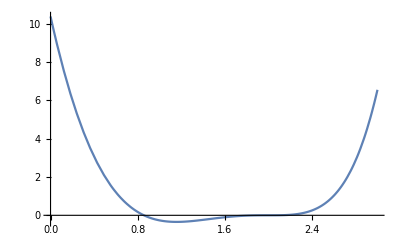

```mathematica
Plot[f[x],{x,0,3}]
```

```mathematica
f'[2]
```

0

```mathematica
f''[2]
```

0

```mathematica
f'''[2]
```

16